```mathematica
z[x_,y_]:=((x^2-y^2)+I*(x*y))^1
```

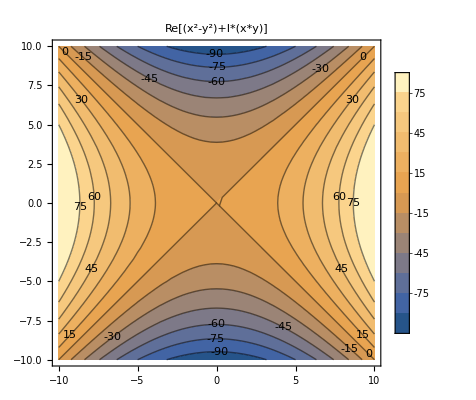

```mathematica
ContourPlot[Re[z[x,y]],{x,-10,10},{y,-10,10},PlotLabel->"Re[(x^2-y^2)+I*(x*y)]",
ContourLabels->True,
PlotLegends->Automatic,
Contours->12,
Axes->True
]
```

```mathematica
Plot3D[Re[z[x,y]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

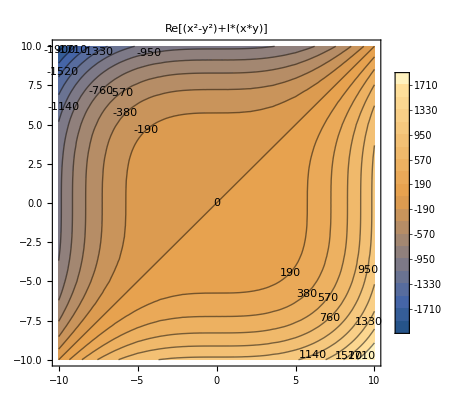

```mathematica
ContourPlot[x^3-y^3,{x,-10,10},{y,-10,10},PlotLabel->"Re[(x^2-y^2)+I*(x*y)]",
ContourLabels->True,
PlotLegends->Automatic,
Contours->20,
Axes->True
]
```

```mathematica
Plot3D[x^3-y^3,{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
10*Log[x]-x
```

-x+10 Log[x]

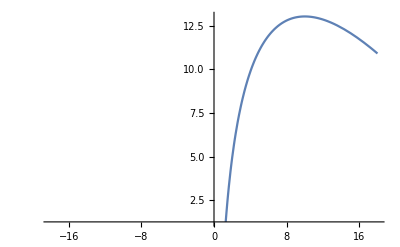

```mathematica
Plot[-x+10 Log[x],{x,-18.,18.}]
```

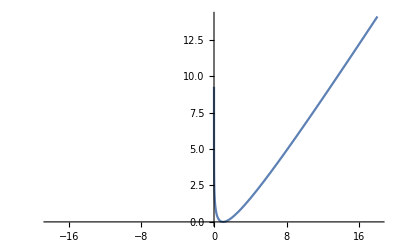

```mathematica
Plot[-1+u-Log[u],{u,-18.,18.}]
```

```mathematica
Limit[(√(u-1-Log[u]))/(u-1),u-> 1,Direction->"FromAbove"]
```

1/(√2)

```mathematica
Limit[1/(2!)*D[((u-1)/(√(u-1-Log[u])))^2,{u,1}],u-> 1,Direction->"FromBelow"]
```

2/3

```mathematica
Limit[1/(1!)*D[((u-1)/(√(u-1-Log[u])))^1,{u,0}],u-> 1,Direction->"FromBelow"]
```

-√2

```mathematica
Limit[1/(3!)*D[((u-1)/(√(u-1-Log[u])))^3,{u,2}],u-> 1,Direction->"FromBelow"]
```

-1/(9 √2)

```mathematica
Limit[1/(4!)*D[((u-1)/(√(u-1-Log[u])))^4,{u,3}],u-> 1,Direction->"FromBelow"]
```

-2/135

```mathematica
Limit[1/(5!)*D[((u-1)/(√(u-1-Log[u])))^5,{u,4}],u-> 1,Direction->"FromBelow"]
```

-1/(540 √2)

```mathematica
Integrate[E^(-s*t^2)*((√2)/216*t^4),{t,-∞,∞}]
```

ConditionalExpression[(√(π/2))/(144 s^(5/2)),Re[s]>0]

```mathematica
s^(s+1)*E^-s*(√((2π)/s)+(√(2π))/(12*s^(3/2))+(√(2π))/(288*s^(5/2)))/.s-> 3/2
```

(685 √(π/2))/(144 ⅇ^(3/2))

```mathematica
N[(685 √(π/2))/(144 ⅇ^(3/2))]
```

1.33029

```mathematica
N[85/72 √(π/(2 ⅇ))]
```

0.897427

```mathematica
N[(164/135+(85 √π)/72)/(2 √(2 ⅇ))]
```

0.70922

```mathematica
N[(196/135+(85 √π)/72)/(2 √(2 ⅇ))]
```

0.76005

```mathematica
2*s^(s+1)*E^-s*(√(π/(2*s))+(√(π/2))/(12*s^(3/2))+(√(π/2))/(288*s^(5/2)))/.s-> 1/2
```

85/72 √(π/(2 ⅇ))

```mathematica
N[85/72 √(π/(2 ⅇ))]
```

0.897427

```mathematica
N[(√π)/2]
```

0.886227

```mathematica
s^(s+1)*E^-s*(√(π/(2*s))+2/(3s)+(√(π/2))/(12*s^(3/2))-4/(135*s^2)+(√(π/2))/(288*s^(5/2)))/.s-> 3/2
```

(9 √(3/2) (524/1215+(685 √(π/3))/648))/(4 ⅇ^(3/2))

```mathematica
N[(9 √(3/2) (524/1215+(685 √(π/3))/648))/(4 ⅇ^(3/2))]
```

0.930325

```mathematica
3*(√π)/4
```

(3 √π)/4

```mathematica
N[(3 √π)/4]
```

1.32934

```mathematica
2*s^(s+1)*E^-s*(√(π/(2*s))+(√(π/2))/(12*s^(3/2))+(√(π/2))/(288*s^(5/2)))/.s-> 3/2
```

(685 √(π/2))/(144 ⅇ^(3/2))

```mathematica
N[(685 √(π/2))/(144 ⅇ^(3/2))]
```

1.33029